# Load Files

```mathematica
SetDirectory[NotebookDirectory[]];

Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
Get[FileNameJoin[{Directory[],"DifferentialOperator.m"}]];
$P=2^31-1;
PureIntegrals=ReadList[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasis1-151.txt"}]];

(*LaportaBasis=ReadList[FileNameJoin[{Directory[],"masters"}]];
LaportaBasis=Cases[LaportaBasis,_ptb,Infinity];*)
```

# Generate Phase-Space Point

```mathematica
tPoint=GetRandomPT[0,$P]
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
(*samplepoint=1;
SubReduList=Get[ToString[StringForm["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone/KIRA/splitres/phasespace_00002.m",IntegerString[samplepoint,10,5]]]];
tPoint=Thread[Rule[invariants,SubReduList[[2,1]]]]

reductionRules=ReductionRules=GetReductionTableFromList[SubReduList[[2,2]]];*)


epsrepl={(ep->(4-d)/2)/.tPoint};
PureIntegralN=Expand[PureIntegrals/.tPoint/.epsrepl/.root[n_]:>PowerMod[n,1/2,$P],Modulus->$P]//EchoTiming;
diffOp=getDifferentialOperator[tPoint];
checkDifferentialOperator[tPoint,diffOp]
```

{d→1385400805,mt2→1839046549,s12→45315412,s123→1041607433,s16→316443122,s23→1813346139,s234→524237384,s34→1845747125,s345→1736619103,s45→1133187590,s56→1970659698}

0.256553

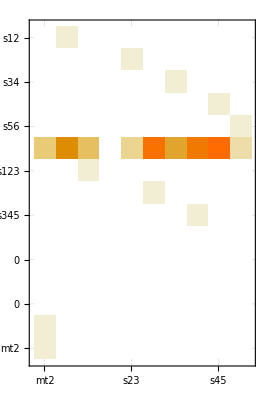

Δ6=0

∂_(RowBox[{) Δ6=0

∂_(RowBox[{) Δ6=0

∂_(RowBox[{) Δ6=0

«7 more identical outputs»

```mathematica
Cases[PureIntegralN3,_hxb,Infinity]//DeleteDuplicates//Length
NonZeros//Length
```

277

5890

# Compute Basis Change Matrix

241

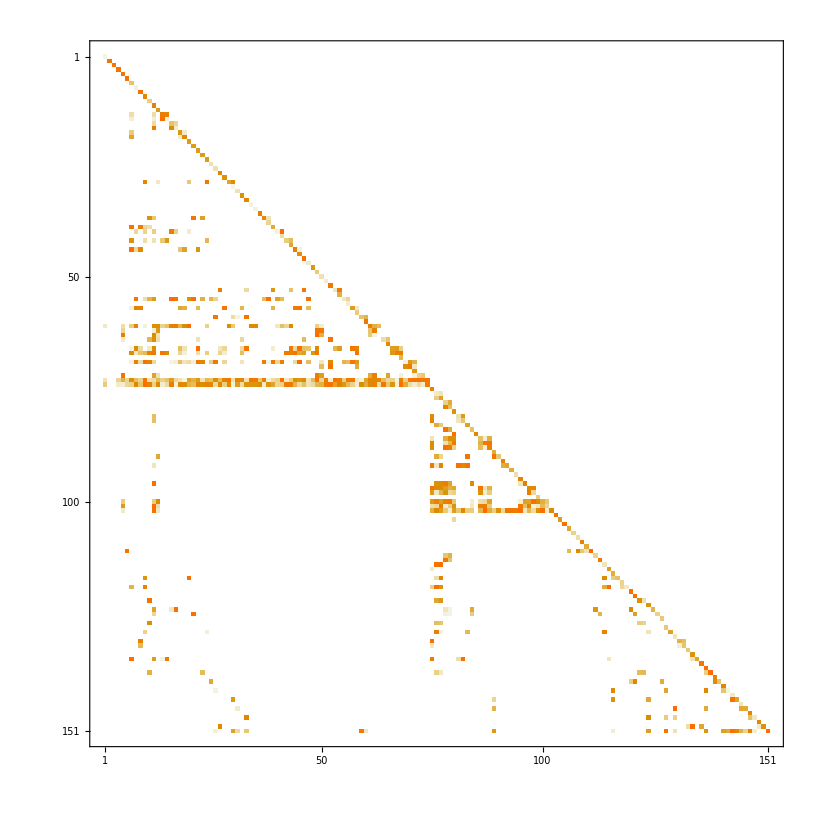

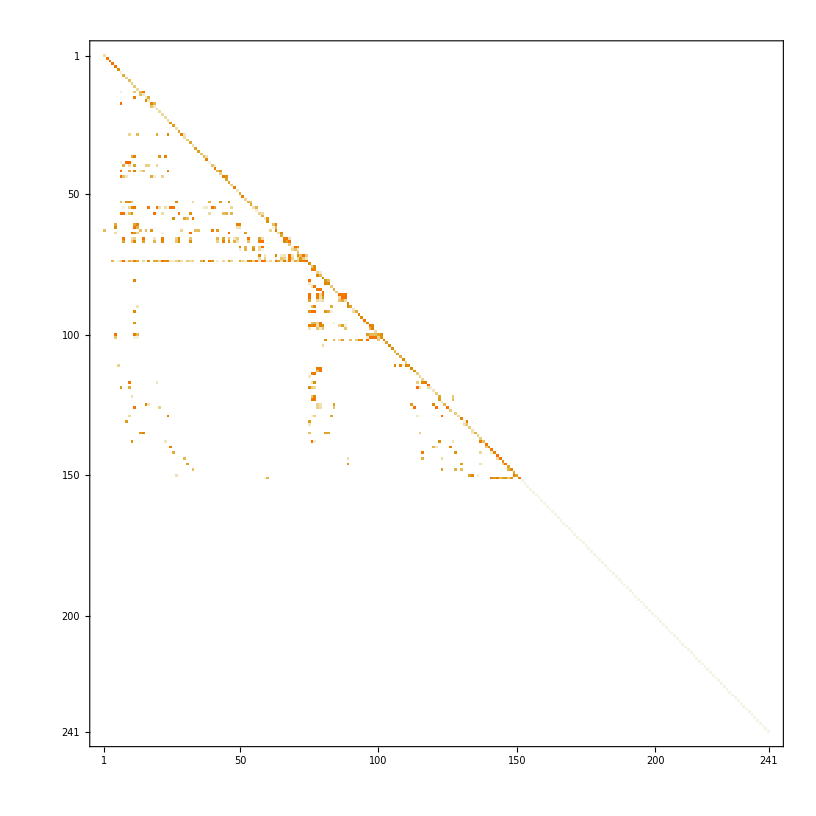

```mathematica
reductionRules=GetReductionTableFromFile[FileNameJoin[{NotebookDirectory[],"KIRA/results/hxb/numerics_2147483647_0.m"}]];
Ureduce=ReadList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];
ExtraRelations=GetExtraRelationReplacements[reductionRules,tPoint];
PureIntegralN2=Expand[PureIntegralN/.reductionRules,Modulus->$P];
PureIntegralN3=Expand[PureIntegralN2/.ExtraRelations,Modulus->$P];

NonZeros=Cases[reductionRules,_hxb,Infinity]//DeleteDuplicates;
ZeroInts=Complement[Ureduce,NonZeros];
ZeroIntsRepl=Thread[Rule[ZeroInts,0]];
PureIntegralN4=Expand[PureIntegralN3/.ExtraRelations/.ZeroIntsRepl,Modulus->$P];
Cases[PureIntegralN4,_hxb,Infinity]//DeleteDuplicates//Length
SubLaporta=Cases[PureIntegralN4,_hxb,Infinity]//DeleteDuplicates;

PureIntegralN4=Expand[PureIntegralN4/.epsrepl,Modulus->$P];

BasisChangMat=Table[CoefficientArrays[PureIntegralN4[[pos]],SubLaporta],{pos,1,Length[PureIntegralN]}];
BasisChangMat=Normal[BasisChangMat[[All,2]]];
BasisChangMatInv=Inverse[BasisChangMat,Modulus->$P];
BasisChangMat[[;;151,;;151]]//MatrixPlot
BasisChangMatInv//MatrixPlot
```

# Compute DE Matrix Pre IBP

```mathematica
loopMomentumScalarProductsT=Expand[loopMomentumScalarProducts/.tPoint,Modulus->$P];
mandelstamScalarProductsT=Expand[mandelstamScalarProducts/.tPoint,Modulus->$P];
DeleteList=Delete[{1,2,3,4,5,6,7,8,9,10,11},Position[tPoint[[All,1]],s16]];
Monitor[diffInts=Table[
Expand[Expand[(applyDifferentialOperator[Collect[Coefficient[diffOp,ds[invariantsnodUpperCase[[var]]]],del[___]],Expand[PureIntegrals[[intpos]]/.tPoint[[DeleteCases[DeleteList,var+1]]]/.epsrepl,Modulus->$P]]/.tPoint/.root'[x_]:>1/(2 root[x]))/.root[x_]:>PowerMod[x,1/2,$P],Modulus->$P]/.loopMomentumScalarProductsT/.mandelstamScalarProductsT,Modulus->$P],{var,1,Length[invariantsnodUpperCase]},{intpos,1,Length[PureIntegrals]}],Row[{ProgressIndicator[(var-1)*241+intpos,{1,241*10}],"  ",var,"/10 ",intpos,"/241"}]];
```

## Extra Step If Redu List does not exit yet

```mathematica
ToReduce=Cases[diffInts,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}],ToReduce];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}]];

ToReduce2=Cases[PureIntegralN,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}],ToReduce2];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];

GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/ExtraRelationsReduList.txt"}]];

DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
WriteJobFile[{"ExtraRelationsReduList","UReduList","ReduList"}]
(*WriteJobFile[{"ExtraRelationsReduList","UReduList"}]*)
```

9621

820

# Apply IBP Reduction

```mathematica
diffIntsIBREDUCED=Expand[diffInts/.reductionRules/.ExtraRelations,Modulus->$P];
NonReduced=Cases[diffIntsIBREDUCED,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
NullInts2=Complement[NonReduced,SubLaporta];
diffIntsIBREDUCED=diffIntsIBREDUCED/.Thread[Rule[NullInts2,0]];
```

499

# Compute DE Matrices

```mathematica
dhxbMatrices=Table[Normal[CoefficientArrays[diffIntsIBREDUCED[[i,j]],SubLaporta]/.{0}->{0,ConstantArray[0,Length[PureIntegralN]]}][[2]],{i,1,Length[invariants]-1},{j,1,Length[SubLaporta]}];
Mplot1=MatrixPlot[Expand[dhxbMatrices[[1]].BasisChangMatInv,Modulus->$P]];
Mplot2=MatrixPlot[Expand[dhxbMatrices[[2]].BasisChangMatInv,Modulus->$P]];
Mplot3=MatrixPlot[Expand[dhxbMatrices[[3]].BasisChangMatInv,Modulus->$P]];
Mplot4=MatrixPlot[Expand[dhxbMatrices[[4]].BasisChangMatInv,Modulus->$P]];
Mplot5=MatrixPlot[Expand[dhxbMatrices[[5]].BasisChangMatInv,Modulus->$P]];
Mplot6=MatrixPlot[Expand[dhxbMatrices[[6]].BasisChangMatInv,Modulus->$P]];
Mplot7=MatrixPlot[Expand[dhxbMatrices[[7]].BasisChangMatInv,Modulus->$P]];
Mplot8=MatrixPlot[Expand[dhxbMatrices[[8]].BasisChangMatInv,Modulus->$P]];
Mplot9=MatrixPlot[Expand[dhxbMatrices[[9]].BasisChangMatInv,Modulus->$P]];
Mplot10=MatrixPlot[Expand[dhxbMatrices[[10]].BasisChangMatInv,Modulus->$P]];
GraphicsGrid[{{Mplot1,Mplot2,Mplot3,Mplot4,Mplot5},{Mplot6,Mplot7,Mplot8,Mplot9,Mplot10}}]
```

-Graphics-

# Acceleration

```mathematica
PureIntegrals[[153]]
```

hxb[-1,1,1,1,0,0,1,1,1,0,0,0,0]

```mathematica
DiffInts=Cases[PureIntegralN,_hxb,Infinity]//EchoFunction[Length];
```

1074

```mathematica
delHXB[p1]DiffInts
delHXB[mt2]DiffInts
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,hxb[1,0,0,1,0,0,0,2,0,0,0,0,0],2 hxb[0,2,0,1,0,0,0,3,0,0,0,0,0],2 hxb[0,2,0,1,0,0,0,3,0,0,0,0,0],hxb[0,2,0,2,0,0,0,2,0,0,0,0,0],2 hxb[0,0,2,1,0,0,0,3,0,0,0,0,0],2 hxb[0,0,2,1,0,0,0,3,0,0,0,0,0],hxb[0,0,2,2,0,0,0,2,0,0,0,0,0],hxb[1,0,1,0,0,0,0,2,0,0,0,0,0],hxb[1,0,0,2,1,0,0,2,0,0,0,0,0],2 hxb[1,0,0,1,1,0,0,3,0,0,0,0,0],hxb[1,0,0,2,1,0,0,2,0,0,0,0,0],hxb[0,1,0,2,1,0,0,2,0,0,0,0,0],hxb[0,0,1,2,0,0,0,2,1,0,0,0,0],2 hxb[1,0,1,0,1,0,0,3,0,0,0,0,0],2 hxb[1,0,1,1,0,0,0,3,0,0,0,0,0],hxb[1,0,1,2,0,0,0,2,0,0,0,0,0],2 hxb[1,0,1,1,0,0,0,3,0,0,0,0,0],hxb[1,0,1,2,0,0,0,2,0,0,0,0,0],2 hxb[2,0,1,1,0,0,0,3,0,0,0,0,0],hxb[0,1,0,1,1,0,0,2,1,0,0,0,0],hxb[0,1,0,2,1,0,0,2,1,0,0,0,0],hxb[1,1,0,1,1,0,0,2,0,0,0,0,0],hxb[1,1,0,2,1,0,0,2,0,0,0,0,0],hxb[1,0,1,0,1,0,0,2,1,0,0,0,0],hxb[1,0,1,1,1,0,0,2,0,0,0,0,0],hxb[0,1,1,1,0,0,0,2,1,0,0,0,0],hxb[0,1,1,2,0,0,0,2,1,0,0,0,0],2 hxb[1,1,1,1,0,0,0,3,0,0,0,0,0],2 hxb[1,1,1,1,0,0,0,3,0,0,0,0,0],hxb[1,1,1,2,0,0,0,2,0,0,0,0,0],hxb[1,1,1,1,1,0,0,2,0,0,0,0,0],hxb[1,1,1,1,1,0,0,2,1,0,0,0,0],hxb[1,1,1,1,1,0,0,2,1,0,0,0,-1],hxb[0,1,0,2,1,0,0,2,1,0,0,0,0],hxb[0,1,1,1,1,0,0,2,1,0,0,0,0],hxb[0,1,1,2,0,0,0,2,1,0,0,0,0],hxb[1,1,0,1,1,0,0,2,1,0,0,0,0],hxb[1,1,1,1,1,0,0,2,1,-1,0,0,0],hxb[1,1,1,1,1,0,0,2,1,0,-1,0,0],hxb[1,1,1,1,1,0,0,2,1,0,0,-1,0],hxb[1,1,1,1,1,0,0,2,1,0,0,0,0],hxb[1,0,1,0,0,0,1,2,1,0,0,0,0],hxb[1,0,1,0,0,0,0,2,0,0,0,0,0],hxb[1,0,1,0,0,1,0,2,0,0,0,0,0],hxb[1,0,1,0,0,1,0,2,1,0,0,0,0],hxb[1,0,1,0,0,1,1,2,1,0,0,0,0],hxb[1,0,1,0,1,0,1,2,0,0,0,0,0],hxb[1,0,1,0,1,0,1,2,1,0,0,0,0],hxb[1,0,1,0,1,1,0,2,1,0,0,0,0],hxb[1,0,1,0,1,1,1,2,0,0,0,0,0],hxb[1,0,1,0,-1,1,1,2,1,0,0,0,0],hxb[1,0,1,0,0,0,1,2,1,0,0,0,0],hxb[1,0,1,0,0,1,0,2,1,0,0,0,0],0,hxb[1,0,1,0,0,1,1,2,0,0,0,0,0],hxb[1,0,1,0,0,1,1,2,1,0,0,0,0],hxb[1,0,1,0,1,-1,1,2,1,0,0,0,0],hxb[1,0,1,0,1,0,0,2,1,0,0,0,0],0,hxb[1,0,1,0,1,0,1,2,0,0,0,0,0],hxb[1,0,1,0,1,0,1,2,1,0,0,0,0],hxb[1,0,1,0,1,1,-1,2,1,0,0,0,0],0,hxb[1,0,1,0,1,1,0,2,0,0,0,0,0],hxb[1,0,1,0,1,1,0,2,1,0,0,0,0],-hxb[1,0,1,0,1,1,1,0,1,0,0,0,0],0,0,hxb[1,0,1,0,1,1,1,2,-1,0,0,0,0],hxb[1,0,1,0,1,1,1,2,0,0,0,0,0],hxb[1,0,1,0,1,1,1,2,1,0,0,0,0],hxb[0,0,2,1,0,0,1,2,0,0,0,0,0],hxb[0,0,2,1,0,1,0,2,0,0,0,0,0],hxb[0,2,0,1,0,0,1,2,0,0,0,0,0],hxb[2,0,0,1,0,0,1,2,0,0,0,0,0],hxb[0,1,0,1,0,0,1,2,1,0,0,0,0],hxb[0,2,0,1,0,0,1,2,1,0,0,0,0],hxb[1,1,0,1,0,0,1,2,0,0,0,0,0],2 hxb[1,1,0,1,0,0,1,3,0,0,0,0,0],hxb[0,0,1,1,0,0,1,2,1,0,0,0,0],hxb[0,0,1,1,0,1,0,2,1,0,0,0,0],hxb[0,2,0,1,0,1,0,2,0,0,0,0,0],hxb[0,1,0,1,1,0,1,2,0,0,0,0,0],hxb[0,0,2,1,0,0,1,2,1,0,0,0,0],hxb[0,0,2,1,0,1,0,2,1,0,0,0,0],hxb[0,0,1,1,0,1,1,2,0,0,0,0,0],2 hxb[0,1,0,1,0,1,0,3,0,0,0,0,0],hxb[0,2,0,1,0,1,0,2,0,0,0,0,0],hxb[0,1,0,1,0,1,1,2,0,0,0,0,0],hxb[0,2,0,1,1,0,1,2,0,0,0,0,0],hxb[0,1,0,1,1,1,0,2,0,0,0,0,0],hxb[2,0,0,1,0,1,0,2,0,0,0,0,0],2 hxb[1,0,0,1,0,1,0,3,0,0,0,0,0],hxb[2,0,0,1,0,1,0,2,0,0,0,0,0],hxb[1,0,0,1,0,1,1,2,0,0,0,0,0],hxb[1,0,0,1,1,0,1,2,0,0,0,0,0],hxb[2,0,0,1,1,0,1,2,0,0,0,0,0],hxb[1,0,0,1,1,1,0,2,0,0,0,0,0],hxb[0,1,0,1,0,1,0,2,1,0,0,0,0],hxb[0,2,0,1,0,1,0,2,1,0,0,0,0],hxb[0,0,1,1,0,1,1,2,1,0,0,0,0],hxb[0,0,2,1,-2,1,1,2,1,0,0,0,0],hxb[0,0,2,1,-1,0,1,2,1,0,0,0,0],hxb[0,0,2,1,-1,1,0,2,1,0,0,0,0],0,hxb[0,0,2,1,-1,1,1,2,0,0,0,0,0],hxb[0,0,2,1,-1,1,1,2,1,0,0,0,0],hxb[0,0,2,1,0,-1,1,2,1,0,0,0,0],hxb[0,0,2,1,0,0,0,2,1,0,0,0,0],0,hxb[0,0,2,1,0,0,1,2,0,0,0,0,0],hxb[0,0,2,1,0,0,1,2,1,0,0,0,0],hxb[0,0,2,1,0,1,-1,2,1,0,0,0,0],0,hxb[0,0,2,1,0,1,0,2,0,0,0,0,0],hxb[0,0,2,1,0,1,0,2,1,0,0,0,0],-hxb[0,0,2,1,0,1,1,0,1,0,0,0,0],0,0,hxb[0,0,2,1,0,1,1,2,-1,0,0,0,0],hxb[0,0,2,1,0,1,1,2,0,0,0,0,0],hxb[0,0,2,1,0,1,1,2,1,0,0,0,0],hxb[0,1,0,1,0,1,1,2,1,0,0,0,0],hxb[0,2,0,1,0,-1,1,2,1,0,0,0,0],hxb[0,2,0,1,0,0,0,2,1,0,0,0,0],0,hxb[0,2,0,1,0,0,1,2,0,0,0,0,0],hxb[0,2,0,1,0,0,1,2,1,0,0,0,-1],hxb[0,2,0,1,0,0,1,2,1,0,0,0,0],hxb[0,2,0,1,0,1,-1,2,1,0,0,0,0],0,hxb[0,2,0,1,0,1,0,2,0,0,0,0,0],hxb[0,2,0,1,0,1,0,2,1,0,0,0,-1],hxb[0,2,0,1,0,1,0,2,1,0,0,0,0],-hxb[0,2,0,1,0,1,1,0,1,0,0,0,0],0,0,0,hxb[0,2,0,1,0,1,1,2,-1,0,0,0,0],hxb[0,2,0,1,0,1,1,2,0,0,0,0,-1],hxb[0,2,0,1,0,1,1,2,0,0,0,0,0],hxb[0,2,0,1,0,1,1,2,1,0,0,0,-2],hxb[0,2,0,1,0,1,1,2,1,0,0,0,-1],hxb[0,2,0,1,0,1,1,2,1,0,0,0,0],hxb[0,1,0,1,1,0,1,2,1,0,0,0,0],hxb[0,2,0,1,-1,0,1,2,1,0,0,0,0],hxb[0,2,0,1,0,0,0,2,1,0,0,0,0],0,hxb[0,2,0,1,0,0,1,2,0,0,0,0,0],hxb[0,2,0,1,0,0,1,2,1,0,0,0,-1],hxb[0,2,0,1,0,0,1,2,1,0,0,0,0],hxb[0,2,0,1,1,0,-1,2,1,0,0,0,0],0,hxb[0,2,0,1,1,0,0,2,0,0,0,0,0],hxb[0,2,0,1,1,0,0,2,1,0,0,0,-1],hxb[0,2,0,1,1,0,0,2,1,0,0,0,0],-hxb[0,2,0,1,1,0,1,0,1,0,0,0,0],0,0,0,hxb[0,2,0,1,1,0,1,2,-1,0,0,0,0],hxb[0,2,0,1,1,0,1,2,0,0,0,0,-1],hxb[0,2,0,1,1,0,1,2,0,0,0,0,0],hxb[0,2,0,1,1,0,1,2,1,0,0,0,-2],hxb[0,2,0,1,1,0,1,2,1,0,0,0,-1],hxb[0,2,0,1,1,0,1,2,1,0,0,0,0],hxb[0,1,0,1,1,1,0,2,1,0,0,0,0],hxb[0,2,0,1,-1,1,0,2,1,0,0,0,0],hxb[0,2,0,1,0,0,0,2,1,0,0,0,0],0,hxb[0,2,0,1,0,1,0,2,0,0,0,0,0],hxb[0,2,0,1,0,1,0,2,1,0,0,0,-1],hxb[0,2,0,1,0,1,0,2,1,0,0,0,0],hxb[0,2,0,1,1,-1,0,2,1,0,0,0,0],0,hxb[0,2,0,1,1,0,0,2,0,0,0,0,0],hxb[0,2,0,1,1,0,0,2,1,0,0,0,-1],hxb[0,2,0,1,1,0,0,2,1,0,0,0,0],-hxb[0,2,0,1,1,1,0,0,1,0,0,0,0],0,0,0,hxb[0,2,0,1,1,1,0,2,-1,0,0,0,0],hxb[0,2,0,1,1,1,0,2,0,0,0,0,-1],hxb[0,2,0,1,1,1,0,2,0,0,0,0,0],hxb[0,2,0,1,1,1,0,2,1,0,0,0,-2],hxb[0,2,0,1,1,1,0,2,1,0,0,0,-1],hxb[0,2,0,1,1,1,0,2,1,0,0,0,0],hxb[0,1,0,1,1,1,1,2,0,0,0,0,0],hxb[0,2,0,1,-1,1,1,2,0,0,0,0,0],hxb[0,2,0,1,0,0,1,2,0,0,0,0,0],hxb[0,2,0,1,0,1,0,2,0,0,0,0,0],0,hxb[0,2,0,1,0,1,1,2,0,0,0,0,-1],hxb[0,2,0,1,0,1,1,2,0,0,0,0,0],hxb[0,2,0,1,1,-1,1,2,0,0,0,0,0],hxb[0,2,0,1,1,0,0,2,0,0,0,0,0],0,hxb[0,2,0,1,1,0,1,2,0,0,0,0,-1],hxb[0,2,0,1,1,0,1,2,0,0,0,0,0],hxb[0,2,0,1,1,1,-1,2,0,0,0,0,0],0,hxb[0,2,0,1,1,1,0,2,0,0,0,0,-1],hxb[0,2,0,1,1,1,0,2,0,0,0,0,0],-hxb[0,2,0,1,1,1,1,0,0,0,0,0,0],0,0,hxb[0,2,0,1,1,1,1,2,-1,0,0,0,0],hxb[0,2,0,1,1,1,1,2,0,0,0,0,-2],hxb[0,2,0,1,1,1,1,2,0,0,0,0,-1],hxb[0,2,0,1,1,1,1,2,0,0,0,0,0],hxb[1,0,0,1,1,1,1,2,0,0,0,0,0],hxb[2,0,0,1,-1,1,1,2,0,0,0,0,0],hxb[2,0,0,1,0,0,1,2,0,0,0,0,0],hxb[2,0,0,1,0,1,0,2,0,0,0,0,0],0,hxb[2,0,0,1,0,1,1,2,-1,0,0,0,0],hxb[2,0,0,1,0,1,1,2,0,0,0,0,0],hxb[2,0,0,1,1,-1,1,2,0,0,0,0,0],hxb[2,0,0,1,1,0,0,2,0,0,0,0,0],0,hxb[2,0,0,1,1,0,1,2,-1,0,0,0,0],hxb[2,0,0,1,1,0,1,2,0,0,0,0,0],hxb[2,0,0,1,1,1,-1,2,0,0,0,0,0],0,hxb[2,0,0,1,1,1,0,2,-1,0,0,0,0],hxb[2,0,0,1,1,1,0,2,0,0,0,0,0],-hxb[2,0,0,1,1,1,1,0,0,0,0,0,0],0,0,hxb[2,0,0,1,1,1,1,2,-2,0,0,0,0],hxb[2,0,0,1,1,1,1,2,-1,0,0,0,0],hxb[2,0,0,1,1,1,1,2,0,0,0,0,0],hxb[0,1,0,1,-1,1,1,2,1,0,0,0,0],hxb[0,1,0,1,0,0,1,2,1,0,0,0,0],hxb[0,1,0,1,0,1,0,2,1,0,0,0,0],0,hxb[0,1,0,1,0,1,1,2,0,0,0,0,0],hxb[0,1,0,1,0,1,1,2,1,0,0,0,0],hxb[0,1,0,1,1,-1,1,2,1,0,0,0,0],hxb[0,1,0,1,1,0,0,2,1,0,0,0,0],0,hxb[0,1,0,1,1,0,1,2,0,0,0,0,0],hxb[0,1,0,1,1,0,1,2,1,0,0,0,0],hxb[0,1,0,1,1,1,-1,2,1,0,0,0,0],0,hxb[0,1,0,1,1,1,0,2,0,0,0,0,0],hxb[0,1,0,1,1,1,0,2,1,0,0,0,0],-hxb[0,1,0,1,1,1,1,0,1,0,0,0,0],0,0,hxb[0,1,0,1,1,1,1,2,-1,0,0,0,0],hxb[0,1,0,1,1,1,1,2,0,0,0,0,0],hxb[0,1,0,1,1,1,1,2,1,0,0,0,0],hxb[-1,1,1,1,0,0,1,2,0,0,0,0,0],hxb[-1,1,1,1,0,0,1,2,1,0,0,0,0],hxb[-1,1,1,1,0,1,0,2,0,0,0,0,0],hxb[-1,1,1,1,0,1,0,2,1,0,0,0,0],hxb[-1,1,1,1,0,1,1,2,0,0,0,0,0],hxb[-1,1,1,1,0,1,1,2,1,0,0,0,0],hxb[0,1,1,1,0,0,1,2,0,0,0,0,0],hxb[0,1,1,1,0,0,1,2,1,0,0,0,0],hxb[0,1,1,1,0,1,0,2,0,0,0,0,0],hxb[0,1,1,1,0,1,0,2,1,0,0,0,0],hxb[0,1,1,1,0,1,1,2,0,0,0,0,0],hxb[1,-1,1,1,0,0,1,2,0,0,0,0,0],hxb[1,-1,1,1,0,1,0,2,0,0,0,0,0],hxb[1,-1,1,1,0,1,1,2,0,0,0,0,0],hxb[1,0,1,1,-1,0,1,2,0,0,0,0,0],hxb[1,0,1,1,-1,1,0,2,0,0,0,0,0],hxb[1,0,1,1,-1,1,1,2,0,0,0,0,0],hxb[1,0,1,1,0,0,1,2,-2,0,0,0,0],hxb[1,0,1,1,0,0,1,2,-1,0,0,0,0],hxb[1,0,1,1,0,0,1,2,0,-1,0,0,0],hxb[1,0,1,1,0,0,1,2,0,0,0,0,0],hxb[1,0,1,1,0,0,1,2,1,0,0,0,0],hxb[1,0,1,1,0,1,0,2,-2,0,0,0,0],hxb[1,0,1,1,0,1,0,2,-1,0,0,0,0],hxb[1,0,1,1,0,1,0,2,0,-1,0,0,0],hxb[1,0,1,1,0,1,0,2,0,0,0,0,0],hxb[1,0,1,1,0,1,0,2,1,0,0,0,0],hxb[1,0,1,1,0,1,1,2,-1,0,0,0,0],hxb[1,0,1,1,0,1,1,2,0,-1,0,0,0],hxb[1,0,1,1,0,1,1,2,0,0,-1,0,0],hxb[1,0,1,1,0,1,1,2,0,0,0,0,0],hxb[1,0,1,1,0,1,1,2,1,0,0,0,0],hxb[1,0,1,1,1,0,1,2,0,0,0,0,0],hxb[1,0,1,1,1,1,0,2,0,0,0,0,0],hxb[1,0,1,1,1,1,1,2,0,0,0,0,0],hxb[1,1,0,1,0,1,0,2,-1,0,0,0,0],hxb[1,1,0,1,0,1,0,2,0,0,0,0,0],hxb[1,1,0,1,0,1,1,2,-1,0,0,0,0],hxb[1,1,0,1,0,1,1,2,0,0,0,0,0],hxb[1,1,0,1,1,0,1,2,-1,0,0,0,0],hxb[1,1,0,1,1,0,1,2,0,0,0,0,0],hxb[1,1,0,1,1,1,0,2,-1,0,0,0,0],hxb[1,1,0,1,1,1,0,2,0,0,0,0,0],hxb[1,1,0,1,1,1,1,2,0,0,0,0,0],hxb[1,1,1,1,-1,0,1,2,0,0,0,0,0],hxb[1,1,1,1,-1,0,1,2,1,0,0,0,0],hxb[1,1,1,1,-1,1,0,2,0,0,0,0,0],hxb[1,1,1,1,-1,1,0,2,1,0,0,0,0],hxb[1,1,1,1,-1,1,1,2,-1,0,0,0,0],hxb[1,1,1,1,-1,1,1,2,0,0,0,0,0],hxb[1,1,1,1,-1,1,1,2,1,0,0,0,0],hxb[1,1,1,1,0,-1,1,2,0,0,0,0,0],hxb[1,1,1,1,0,-1,1,2,1,0,0,0,0],hxb[1,1,1,1,0,0,1,2,-1,0,0,0,0],hxb[1,1,1,1,0,0,1,2,0,-1,0,0,0],hxb[1,1,1,1,0,0,1,2,0,0,0,0,0],hxb[1,1,1,1,0,0,1,2,1,-1,0,0,0],hxb[1,1,1,1,0,0,1,2,1,0,0,0,0],hxb[1,1,1,1,0,1,-1,2,0,0,0,0,0],hxb[1,1,1,1,0,1,-1,2,1,0,0,0,0],hxb[1,1,1,1,0,1,0,2,-1,0,0,0,0],hxb[1,1,1,1,0,1,0,2,0,-1,0,0,0],hxb[1,1,1,1,0,1,0,2,0,0,-1,0,0],hxb[1,1,1,1,0,1,0,2,0,0,0,0,0],hxb[1,1,1,1,0,1,0,2,1,-1,0,0,0],hxb[1,1,1,1,0,1,0,2,1,0,0,0,0],hxb[1,1,1,1,0,1,1,2,-2,0,0,0,0],hxb[1,1,1,1,0,1,1,2,-1,-1,0,0,0],hxb[1,1,1,1,0,1,1,2,0,-1,0,0,0],hxb[1,1,1,1,0,1,1,2,0,0,-1,0,0],hxb[1,1,1,1,0,1,1,2,0,0,0,0,0],hxb[1,1,1,1,0,1,1,2,1,-1,0,0,0],hxb[1,1,1,1,0,1,1,2,1,0,-1,0,0],hxb[1,1,1,1,1,-1,1,2,0,0,0,0,0],hxb[1,1,1,1,1,-1,1,2,1,0,0,0,0],hxb[1,1,1,1,1,0,1,2,-1,0,0,0,0],hxb[1,1,1,1,1,0,1,2,0,-1,0,0,0],hxb[1,1,1,1,1,0,1,2,0,0,0,0,0],hxb[1,1,1,1,1,0,1,2,1,-1,0,0,0],hxb[1,1,1,1,1,0,1,2,1,0,0,0,0],hxb[1,1,1,1,1,1,-1,2,0,0,0,0,0],hxb[1,1,1,1,1,1,-1,2,1,0,0,0,0],hxb[1,1,1,1,1,1,0,2,-1,0,0,0,0],hxb[1,1,1,1,1,1,0,2,0,0,0,0,0],hxb[1,1,1,1,1,1,0,2,1,-1,0,0,0],hxb[1,1,1,1,1,1,0,2,1,0,0,0,0],hxb[1,1,1,1,1,1,1,2,-1,0,0,0,0],hxb[1,1,1,1,1,1,1,2,0,-1,0,0,0],hxb[1,1,1,1,1,1,1,2,0,0,0,0,0],hxb[1,1,1,1,1,1,1,2,1,0,0,0,0]}

```mathematica
LONGInt=Collect[PureIntegrals[[73]],{_hxb,_root,ep},Together]
```

```mathematica
tPointNomt2=Join[Delete[tPoint,{{3},{5}}],epsrepl]
```

{d→966560106,mt2→1148992341,s123→105850019,s23→1129432713,s234→580075961,s34→1689024705,s345→992575504,s45→222126701,s56→781561186,ep→-483280051}

```mathematica
LONGInt2=Collect[Expand[LONGInt/.tPointNomt2,Modulus->$P],{_hxb,_root,ep},Together];
InvanriantPart=Expand[(D[LONGInt2,s12]/.tPoint/.root'[x_]:>1/(2 root[x]))/.root[x_]:>PowerMod[x,1/2,$P],Modulus->$P];
dp1=delHXB[p[1]]DiffInts;
dp2=delHXB[p[2]]DiffInts;
dp3=delHXB[p[3]]DiffInts;
dp4=delHXB[p[4]]DiffInts;
dp5=delHXB[p[5]]DiffInts;
dp6=delHXB[p[6]]DiffInts;
```

```mathematica
Coefficient[diffOp,ds[S12]]/.{del[s12]:>InvanriantPart,del[p[1]]:>dp1[[73]],del[p[2]]:>dp2[[73]],del[p[3]]:>dp3[[73]],del[p[4]]:>dp4[[73]],del[p[5]]:>dp5[[73]],del[p[6]]:>dp6[[73]]};
```

```mathematica
dp1=delHXB[p[1]]DiffInts
```

```mathematica
dp1
```